```mathematica
v0={0,1,1.5,2,3}

u0={413,100,256,90,421}
```

{0,1,1.5,2,3}

{413,100,256,90,421}

```mathematica
Apply[Plus,v0]/4
```

1.875

```mathematica
Apply[Plus,u0]/4
```

320

```mathematica
256/1024
```

1/4

```mathematica
w=Table[{v0[[i]],u0[[i]]/(2*Sqrt[2]*1024.)},{i,5}]
```

{{0,0.142595},{1,0.0345267},{1.5,0.0883883},{2,0.031074},{3,0.145357}}

```mathematica
f[x_]=Fit[w,Table[x^i,{i,0,4}],x]
```

0.142595-0.897176 x+1.40457 x^2-0.738986 x^3+0.123529 x^4

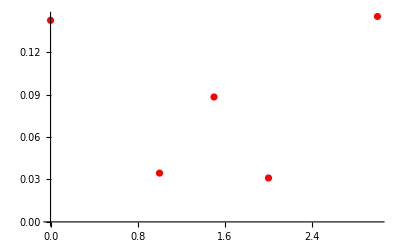

```mathematica
g1=ListPlot[w,PlotStyle->Red, ImageSize->Full]
```

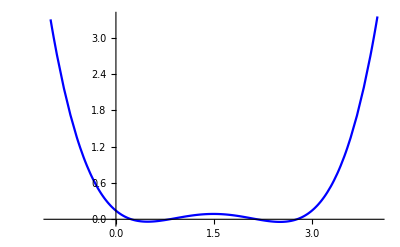

```mathematica
g2=Plot[f[x],{x,-1,4},PlotStyle->Blue, ImageSize->Full,PlotRange->All]
```

```mathematica
f[1.5]
```

0.0883883

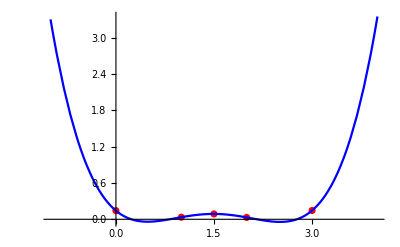

```mathematica
Show[{g1,g2},PlotRange->All]
```